```mathematica
Вариант 3;
```

Задание 1

```mathematica
Начальные данные;
X = {0, Pi/12, Pi/6, Pi/4, Pi/3};
f[x_] = Tan[x];
n = Length[X] - 1;
Do[{Subscript[x, i] = X[[i + 1]], Subscript[f, i] = f[Subscript[x, i]]}, {i, 0, n}]
```

```mathematica
Алгебраический интерполяционный многочлен через определитель Вандермонда;
Unprotect[Power]; 0^0 := 1;
Do[Subscript[fi, j][x_] = x^j, {j, 0, n}];
Do[Subscript[d, i, j] = Subscript[fi, j][Subscript[x, i]], {i, 0, n}, {j, 0, n}];
Do[{Subscript[d, i, n + 1] = Subscript[f, i], Subscript[d, n + 1, i] = Subscript[fi, i][x]}, {i, 0, n}];
Subscript[d, n + 1, n + 1] = 0;
V = Table[Subscript[d, i, j], {i, 0, n}, {j, 0, n}];
V1 = Table[Subscript[d, i, j], {i, 0, n + 1}, {j, 0, n + 1}];
V1 // MatrixForm
P[x_] = -Det[V1]/Det[V] // Expand
```

(1 | 0 | 0 | 0 | 0 | 0
1 | π/12 | π^2/144 | π^3/1728 | π^4/20736 | 2-√3
1 | π/6 | π^2/36 | π^3/216 | π^4/1296 | 1/(√3)
1 | π/4 | π^2/16 | π^3/64 | π^4/256 | 1
1 | π/3 | π^2/9 | π^3/27 | π^4/81 | √3
1 | x | x^2 | x^3 | x^4 | 0)

(112 x)/π-(63 √3 x)/π-(1584 x^2)/π^2+(918 √3 x^2)/π^2+(7200 x^3)/π^3-(4176 √3 x^3)/π^3-(10368 x^4)/π^4+(6048 √3 x^4)/π^4

```mathematica
Интерполяционные условия;
Table[P[Subscript[x, i]] == Subscript[f, i], {i, 0, n}]
```

{True,True,True,True,True}

```mathematica
С помощью встроенной функции InterpolatingPolynomial;
Tbl = Table[{Subscript[x, i], Subscript[f, i]}, {i, 0, n}];
P1[x_] = InterpolatingPolynomial[Tbl, x] // Expand
P[x] == P1[x]
```

(112 x)/π-(63 √3 x)/π-(1584 x^2)/π^2+(918 √3 x^2)/π^2+(7200 x^3)/π^3-(4176 √3 x^3)/π^3-(10368 x^4)/π^4+(6048 √3 x^4)/π^4

True

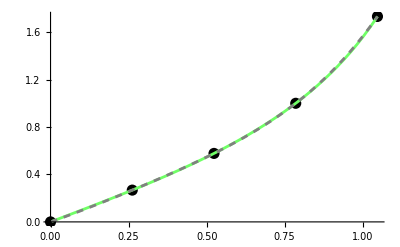

```mathematica
Исходные точки и функция и интерполяционный многочлен;
Gr1 = ListPlot[Tbl, PlotStyle -> {Black, PointSize[0.02]}];
Gr2 = Plot[f[x], {x, Subscript[x, 0], Subscript[x, n]}, PlotStyle -> RGBColor[0.44, 1, 0.4]];
Gr3 = Plot[P[x], {x, Subscript[x, 0], Subscript[x, n]}, PlotStyle -> {Gray, Dashed}];
Show[Gr1, Gr2, Gr3]
```

```mathematica
Приближенное значение;
xx = Pi/9;
P[xx] // N
A = N[Abs[f[xx] - P[xx]], 2]
B = N[(A/(Abs[P[xx]]))*100, 2]
Print["Ответ: приближенное значение ", P[xx] // N, "; абсолютная погрешность ", A, "; относительная погрешность ", B, "%."]
```

Ответ: приближенное значение 0.36549; абсолютная погрешность 0.0015; относительная погрешность 0.42%.

0.36549

0.0015

0.42

Задание 2. Доказать, что функции x, x^2, ..., x^n образуют систему Чебышева на [1, 5]. Найти отрезок, на котором они не являются системой Чебышева.

Доказательство. Любая нетривиальная линейная комбинация имеет вид p(x)=a1 x + a2 x^2 + ... + an x^n = x q(x), где deg q <= n-1. На [1,5] множитель x не обращается в нуль, поэтому число корней p не превосходит числа корней q, то есть не больше n-1. Значит {x,...,x^n} — система Чебышева на [1,5]. На отрезке, содержащем 0, например [-1,1], система не является чебышевской: комбинация x^2-x = x(x-1) имеет два корня.

```mathematica
Проверка определителя для {x,x^2,x^3} в точках на [1,5];
pts = {1, 2, 5};
Det[Table[pts[[i]]^j, {i, 1, 3}, {j, 1, 3}]]
Print["Определитель ненулевой на (1,5)."]
Print["На [-1,1]: x(x-1)=0 имеет корни 0 и 1, больше чем 3-1-1 допустимых для двух функций {x,x^2} при n=2."]
```

Определитель ненулевой на (1,5).

На [-1,1]: x(x-1)=0 имеет корни 0 и 1, больше чем 3-1-1 допустимых для двух функций {x,x^2} при n=2.

120